## Radial Wavefunctions

Recursive implementation of associated Laguerre polynomials:

```mathematica
Laguerre[q_,p_,x_]:=((2q-1+p-x)Laguerre[q-1,p,x]- (q-1+p)Laguerre[q-2,p,x])/q
Laguerre[0,p_,x_]:=1
Laguerre[1,p_,x_]:=1+p-x
```

Compare against Mathematica’s implementation.

```mathematica
Table[Table[Fn[l, m, x]//Expand, {l, 0, 6},{m, 0, l}],{Fn,{LaguerreL, Laguerre}}]//TableForm
```

1 | 1-x
2-x | 1-2 x+x^2/2
3-3 x+x^2/2
6-4 x+x^2/2 | 1-3 x+(3 x^2)/2-x^3/6
4-6 x+2 x^2-x^3/6
10-10 x+(5 x^2)/2-x^3/6
20-15 x+3 x^2-x^3/6 | 1-4 x+3 x^2-(2 x^3)/3+x^4/24
5-10 x+5 x^2-(5 x^3)/6+x^4/24
15-20 x+(15 x^2)/2-x^3+x^4/24
35-35 x+(21 x^2)/2-(7 x^3)/6+x^4/24
70-56 x+14 x^2-(4 x^3)/3+x^4/24 | 1-5 x+5 x^2-(5 x^3)/3+(5 x^4)/24-x^5/120
6-15 x+10 x^2-(5 x^3)/2+x^4/4-x^5/120
21-35 x+(35 x^2)/2-(7 x^3)/2+(7 x^4)/24-x^5/120
56-70 x+28 x^2-(14 x^3)/3+x^4/3-x^5/120
126-126 x+42 x^2-6 x^3+(3 x^4)/8-x^5/120
252-210 x+60 x^2-(15 x^3)/2+(5 x^4)/12-x^5/120 | 1-6 x+(15 x^2)/2-(10 x^3)/3+(5 x^4)/8-x^5/20+x^6/720
7-21 x+(35 x^2)/2-(35 x^3)/6+(7 x^4)/8-(7 x^5)/120+x^6/720
28-56 x+35 x^2-(28 x^3)/3+(7 x^4)/6-x^5/15+x^6/720
84-126 x+63 x^2-14 x^3+(3 x^4)/2-(3 x^5)/40+x^6/720
210-252 x+105 x^2-20 x^3+(15 x^4)/8-x^5/12+x^6/720
462-462 x+165 x^2-(55 x^3)/2+(55 x^4)/24-(11 x^5)/120+x^6/720
924-792 x+(495 x^2)/2-(110 x^3)/3+(11 x^4)/4-x^5/10+x^6/720
1 | 1-x
2-x | 1-2 x+x^2/2
3-3 x+x^2/2
6-4 x+x^2/2 | 1-3 x+(3 x^2)/2-x^3/6
4-6 x+2 x^2-x^3/6
10-10 x+(5 x^2)/2-x^3/6
20-15 x+3 x^2-x^3/6 | 1-4 x+3 x^2-(2 x^3)/3+x^4/24
5-10 x+5 x^2-(5 x^3)/6+x^4/24
15-20 x+(15 x^2)/2-x^3+x^4/24
35-35 x+(21 x^2)/2-(7 x^3)/6+x^4/24
70-56 x+14 x^2-(4 x^3)/3+x^4/24 | 1-5 x+5 x^2-(5 x^3)/3+(5 x^4)/24-x^5/120
6-15 x+10 x^2-(5 x^3)/2+x^4/4-x^5/120
21-35 x+(35 x^2)/2-(7 x^3)/2+(7 x^4)/24-x^5/120
56-70 x+28 x^2-(14 x^3)/3+x^4/3-x^5/120
126-126 x+42 x^2-6 x^3+(3 x^4)/8-x^5/120
252-210 x+60 x^2-(15 x^3)/2+(5 x^4)/12-x^5/120 | 1-6 x+(15 x^2)/2-(10 x^3)/3+(5 x^4)/8-x^5/20+x^6/720
7-21 x+(35 x^2)/2-(35 x^3)/6+(7 x^4)/8-(7 x^5)/120+x^6/720
28-56 x+35 x^2-(28 x^3)/3+(7 x^4)/6-x^5/15+x^6/720
84-126 x+63 x^2-14 x^3+(3 x^4)/2-(3 x^5)/40+x^6/720
210-252 x+105 x^2-20 x^3+(15 x^4)/8-x^5/12+x^6/720
462-462 x+165 x^2-(55 x^3)/2+(55 x^4)/24-(11 x^5)/120+x^6/720
924-792 x+(495 x^2)/2-(110 x^3)/3+(11 x^4)/4-x^5/10+x^6/720

Computations for test cases.

```mathematica
N[Table[LaguerreL[1,0,x],{x,-1,1, 1/2}],15]
```

{2.,1.5,1.,0.5,0}

Hydrogen radial wavefunction, taken from Mathematica’s documentation page for LaguerreL, under the applications heading:

```mathematica
Radial[n_,l_,r_]:=√(((n-l-1)!)/((n+l)!)) ⅇ^(-r/n) ((2r)/n)^l 2/n^2 LaguerreL[n-l-1, 2l+1,(2r)/n]
```

Test case computation.

```mathematica
N[Table[Radial[3, 0,r],{r,{5.708356131145069,5.83783429904662,7.306501771241495,7.507831892414007,3.150506534921816,7.281058025607649,7.624117128371423,9.59925254299943,9.362671469203988,8.227798270360493}}],15]
```

{-0.0224952,-0.0202023,0.00281192,0.00536186,-0.0491676,0.00247796,0.00675915,0.0223802,0.0212521,0.0131223}

Heuristic for estimating maximum size of an orbital:

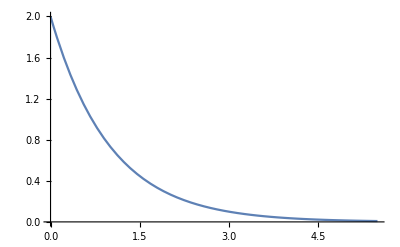
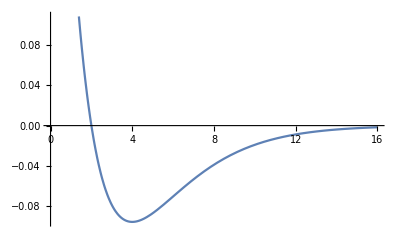
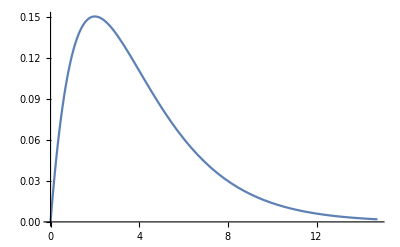
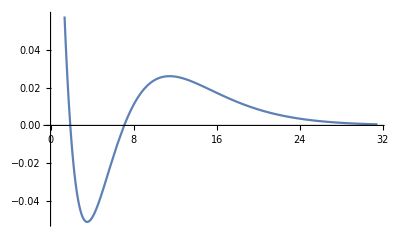
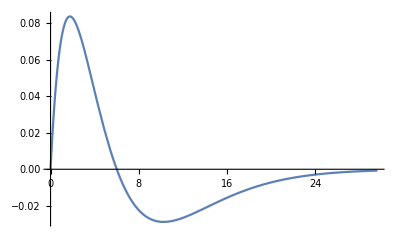
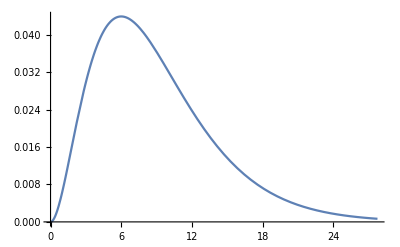
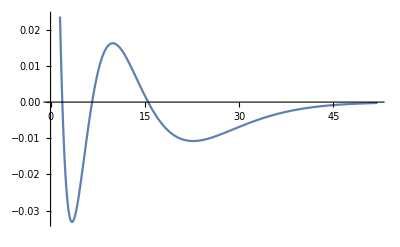
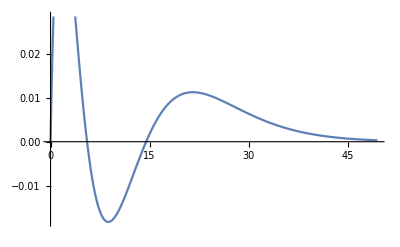
-Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Table[
Plot[Evaluate[Radial[n,l,r]],{r,0,n(5/2 n-5/8 l+3)(*This is the heuristic.*)}],
{n,1,8},
{l,0,n-1}
]//TableForm
```